```mathematica
m=0.5;
ρ=1.2(*1.2*);
r=0.11;
CD=0.47;
ω=10;
v=30;
Subscript[K, D]=1/(2*m)*ρ*CD*π*r^2
Subscript[K, L]=16/(3*m)*π^2*r^3*ω*ρ/v
Subscript[L, 2]=30;
ϵ=Subscript[K, D]*Subscript[L, 2]
Subscript[L, 1]=Subscript[K, L]*Subscript[L, 2]^2
Subscript[K, L]*Subscript[L, 1]
```

0.0214395

0.0560488

0.643185

50.4439

2.82732

```mathematica
y[t_]:=1/Subscript[K, D]*Log[Subscript[K, D]*t*v+1];
x[t_]:=(Log[1+t v Subscript[K, D]] Subscript[K, L])/Subscript[K, D]^2-(t v Subscript[K, L])/Subscript[K, D](*Integrate[Integrate[-Subscript[K, L]*(y'[t])^2,t],t]-t*v*Subscript[K, L]/Subscript[K, D];*)
x[t]
x[0]
x'[0]
y'[0]
```

-78.4284 t+121.938 Log[1+0.643185 t]

0.

1.42109×10^-14

30.

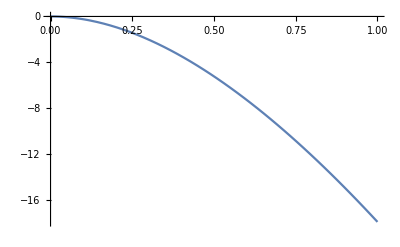

```mathematica
Plot[x[t],{t,0,1}]
```

```mathematica
z[t_]=-(t v Subscript[K, L])/(Subscript[K, D]^2 Subscript[L, 2])+(v (-t+t Log[1+t v Subscript[K, D]]+(2 Log[1+t v Subscript[K, D]])/(v Subscript[K, D])) Subscript[K, L])/(Subscript[K, D]^2 Subscript[L, 2])(*-Integrate[Integrate[y'[t]*x'[t],t],t]/Subscript[L, 2]-(v Subscript[K, L])/(Subscript[K, D]^2 Subscript[L, 2])*t*)
xtot[t_]=x[t]+ϵ*z[t];
```

-121.938 t+121.938 (-t+3.10953 Log[1+0.643185 t]+t Log[1+0.643185 t])

```mathematica
T=1(*1.26*)
x[0]
x'[0]
y[0]
y'[0]
x[T]

z[T]
ϵ

Sqrt[xtot[T]^2+y[T]^2]
```

1

0.

1.42109×10^-14

0.

30.

-17.8698

z[1]

0.643185

√(536.597+xtot[1]^2)

```mathematica
xtot[T]
y[T]
```

-14.6589

23.1646

16.5652 Abs[-0.0483689 x-0.0361205 y]

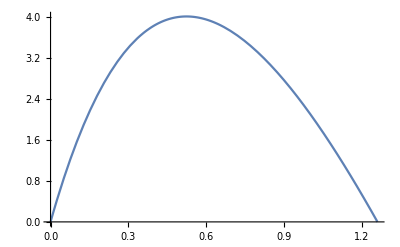

```mathematica
dist[x_,y_]=Abs[x/xtot[T]-y/y[T]]/Sqrt[(1/xtot[T])^2+(1/y[T])^2]
Plot[dist[xtot[t],y[t]],{t,0,T}]
```

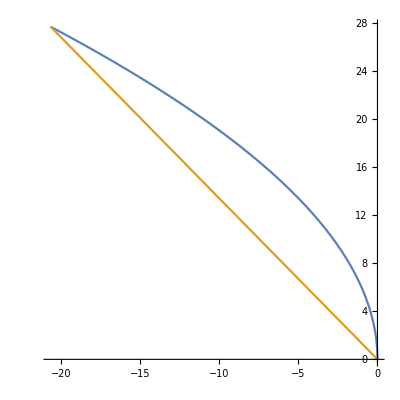

```mathematica
ParametricPlot[{{xtot[t],y[t]},{t/T*xtot[T],t/T*y[T]}},{t,0,T}, AspectRatio->1]
```

```mathematica
y0[t_]=v*t
y1[t_]=-1/(2*Subscript[L, 2])*v^2*t^2
```

t v

-(t^2 v^2)/(2 L_2)

```mathematica
y2[t_]=((2 Log[1+t v Subscript[K, D]]-t v Subscript[K, D] (2-2 Log[1+t v Subscript[K, D]]+t v Subscript[K, D])) Subscript[K, L]^3)/(2 Subscript[K, D]^5 Subscript[L, 1])+(t^3 v^3)/(3 Subscript[L, 2]^2)(*FullSimplify[Integrate[Integrate[-2/Subscript[L, 2]*y1'[t]*y0'[t]+(Subscript[K, L]/Subscript[K, D])^2/Subscript[L, 1]*y0'[t]*x'[t],t],t]]*)
```

((2 Log[1+t v K_D]-t v K_D (2-2 Log[1+t v K_D]+t v K_D)) K_L^3)/(2 K_D^5 L_1)+(t^3 v^3)/(3 L_2^2)

```mathematica
ynew[t_]=y0[t]+ϵ*y1[t]+ϵ^2*y2[t]
```

30 t-9.64777 t^2+0.413686 (10 t^3+385.291 (-0.643185 t (2+0.643185 t-2 Log[1+0.643185 t])+2 Log[1+0.643185 t]))

```mathematica
ynew[0]
```

0.

```mathematica
ynew'[0]
```

30.

```mathematica
ynew[T]
```

13.6624